```mathematica
(*
Import@"https://raw.githubusercontent.com/jkuczm/MathematicaCellsToTeX/master/NoInstall.m"
PacletInstall@"http://github.com/jkuczm/MathematicaCellsToTeX/releases/download/v0.2.2/CellsToTeX-0.2.2.paclet"
*)
Needs@"CellsToTeX`";
```

1

```mathematica
SQRmatrixSize=10;
matrixAentries =Range[1,SQRmatrixSize*SQRmatrixSize];
matrixAentries=ArrayReshape[matrixAentries,{SQRmatrixSize,SQRmatrixSize}];
matrixA=Table[matrixAentries[[i,j]],{i,1,SQRmatrixSize},{j,1,SQRmatrixSize}];
MatrixForm[matrixA]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70
71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90
91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100)

2
matrixA is singular, therefore Inverse[matrixA] does not exist.

3

```mathematica
SQRmatrixSize=30;
matrixB=π*IdentityMatrix[SQRmatrixSize];
MatrixForm[matrixB]
```

(π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π)

3.a & 3.b
Yes, “A triangular matrix (upper, lower or diagonal) is invertible if and only if no element on its main diagonal is 0.”

“by hand” ...
Since, Inverse[A] equals diag(1/a_1,1/a_2,…,1/a_n), Inverse[matrixB] is equal to 1/πIdentityMatrix[30]

Verification with Mathematica is shown below ...

```mathematica
Inverse[matrixB];
MatrixForm[%]
```

(1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/π)

3.c

```mathematica
MatrixRank[matrixB]
```

30

4

```mathematica
SQRmatrixSize=16;
matrixC=Table[0,{i,1,SQRmatrixSize},{j,1,SQRmatrixSize}];
rows=Dimensions[matrixC][[1]];
cols=Dimensions[matrixC][[2]];
For[i=1,i≤ rows,i++,
For[j=1,j≤ cols,j++,
If[i==j,
matrixC[[i,j]]=(π+i)-1,
matrixC[[i,j]]=0];
];
];
MatrixForm[matrixC]
```

(π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1+π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2+π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3+π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4+π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 5+π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 6+π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7+π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8+π | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9+π | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10+π | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11+π | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12+π | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13+π | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14+π | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15+π)

4.a & 4.b
Yes, “A triangular matrix (upper, lower or diagonal) is invertible if and only if no element on its main diagonal is 0.”

“by hand” ...
Since, Inverse[A] equals diag(1/a_1,1/a_2,…,1/a_n), Inverse[matrixB] is equal to 1/((π+i)-1)IdentityMatrix[16]

Verification with Mathematica is shown below ...

```mathematica
Inverse[matrixC];
MatrixForm[%]
```

(1/π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(1+π) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(2+π) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/(3+π) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(4+π) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(5+π) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(6+π) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(7+π) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(8+π) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(9+π) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(10+π) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(11+π) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(12+π) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(13+π) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(14+π) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(15+π))

4.c
Multiplying matrixC times the inverse of matrixC. However, since we know that Inverse[matrixC] exists, the reduced echelon form is the identity matrix (of size 16x16).

```mathematica
MatrixRank[matrixC];
RowReduce[matrixC];
MatrixForm[%]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

5.a

```mathematica
matrixD=({{a, b}, {c, d}});
Inverse[matrixD];
MatrixForm[%]
```

(d/(-b c+a d) | -b/(-b c+a d)
-c/(-b c+a d) | a/(-b c+a d))

5.b
When  a = 2; d = 2; b = 1; c = 4, Inverse[matrixD] does not exist. Mathematica outputs the following error:
⋯ Inverse: Matrix {{2,1},{4,2}} is singular

6.a

```mathematica
Solve[{
x-y==3,
x*π-y*π==3*π
},{x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→-3+x}}

6.b

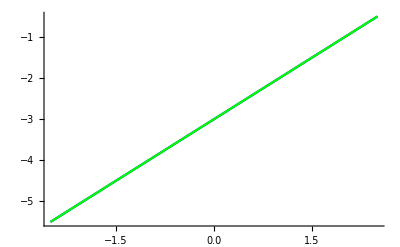

```mathematica
contourLimits=2.5;
(*
ContourPlot[{
x-y==3,
x*π-y*π==3*π
},{x,0.5,1.0},{y,-2.0,-2.5},ContourStyle->{Blue,Orange}]
*)
Show[{
Plot[x-3,{x,-contourLimits,contourLimits},PlotStyle->Blue],
Plot[x-3,{x,-contourLimits,contourLimits},PlotStyle->Green]
},PlotRange->All,AxesOrigin->{0,0}]
```

6.c
The system has infinitely many solutions.

6.d

```mathematica
matrixA=({{1, -1}, {π, -π}});
matrixB=({{3}, {3*π}});
(* rows=m=i *) (* cols=n=j *)
getNumOfSolutions[varA_,varB_]:=Module[{vA=varA,vB=varB,vAB,Arank,ABrank, n},
vAB=ArrayFlatten[{{vA,vB}}];
Arank=MatrixRank[vA];
ABrank=MatrixRank[vAB];
n=Dimensions[vA][[2]];
If[Arank<ABrank,
Print["The system has no solution"];,
If[Arank==ABrank&&Arank<n&&ABrank<n,
Print["The system has infinitely many solutions"];,
If[Arank==ABrank&&Arank==n,
Print["The system has a unique solution"];,
Print["[ERROR] The system has ? solution(s)\n
Beware, if the system is homogeneous (varB is a zero vector and n>m (more variables than equations), then the system has infinitely many solutions)"];
];
];
];
];
getNumOfSolutions[matrixA,matrixB]
```

The system has infinitely many solutions

7.a

```mathematica
contourLimits=5;
(*
ContourPlot3D[{
x+y+z==10,
2/3*x+2/3*y+2/3*z==11,
5/9*x+5/9*y+5/9*z==12
},
{x,-contourLimits,contourLimits},
{y,-contourLimits,contourLimits},
{z,-contourLimits,contourLimits},Axes->True,PlotLegends->"Expressions"]
*)
Show[{
Plot3D[10-x-y,{x,-contourLimits,contourLimits},{y,-contourLimits,contourLimits},PlotStyle->Blue],
Plot3D[1/2 (33-2 x-2 y),{x,-contourLimits,contourLimits},{y,-contourLimits,contourLimits},PlotStyle->Orange],
Plot3D[1/5 (108-5 x-5 y),{x,-contourLimits,contourLimits},{y,-contourLimits,contourLimits},PlotStyle->Green]
},PlotRange->All,AxesOrigin->{0,0}]
```

-Graphics3D-

7.b
7.b.1 normal vector: A nonzero vector that is perpendicular to the plane is called a normal vector to the plane.
7.b.2 The system is inconsistent because the three normal vectors point to the same direction.

7.c

```mathematica
Solve[{
x+y+z==10,
2/3*x+2/3*y+2/3*z==11,
5/9*x+5/9*y+5/9*z==12
},{x,y,z}]
```

{}

7.d & 7.e
The reduced row echelon of A will be (1 | 1 | 1
0 | 0 | 0
0 | 0 | 0), since all the entries are the same within each row. MatrixRank[A]=1

Verification with Mathematica is shown below ...

```mathematica
matrixA=({{1, 1, 1}, {2/3, 2/3, 2/3}, {5/9, 5/9, 5/9}});
matrixB=({{10}, {11}, {12}});
matrixAB=ArrayFlatten[{{matrixA,matrixB}}];
RowReduce[matrixA]
MatrixForm[%]
MatrixRank[matrixA]
```

{{1,1,1},{0,0,0},{0,0,0}}

(1 | 1 | 1
0 | 0 | 0
0 | 0 | 0)

1

7.f

```mathematica
RowReduce[matrixAB];
MatrixForm[%]
MatrixRank[matrixAB]
```

(1 | 1 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

2

7.g

```mathematica
getNumOfSolutions[matrixA,matrixB];
```

The system has no solution

```mathematica
(*
GET LaTeX CODE
*)
nbObj=Notebooks[][[1]];
(*Swich off auto deleting of labels,so that we can extract some data from them.*)CurrentValue[nbObj,CellLabelAutoDelete]=False;
SelectionMove[nbObj,All,Notebook];
(*SelectionEvaluate[nbObj,Before];*)
SetOptions[CellToTeX,"CurrentCellIndex"->Automatic];
ExportString[NotebookGet[nbObj]/.cell:Cell[_,__]:>Cell[CellToTeX[cell],"Final"],"TeX","FullDocument"->False,"ConversionRules"->{"Final"->Identity}]
```

CellsToTeXException::unsupported: CellStyle: Text is not one of supported: Code|Input|Output|Print|Message. Exception occurred in CellToTeX[Cell[
1,Text,CellChangeTimes→{{3.75794×10^9,3.75794×10^9},3.75794×10^9}]].

CellsToTeXException::unsupported: CellStyle: Text is not one of supported: Code|Input|Output|Print|Message. Exception occurred in CellToTeX[Cell[
2
matrixA is singular, therefore Inverse[matrixA] does not exist.,Text,CellChangeTimes→{3.75794×10^9,{3.75794×10^9,3.75794×10^9},{3.75794×10^9,3.75794×10^9}}]].

CellsToTeXException::unsupported: CellStyle: Text is not one of supported: Code|Input|Output|Print|Message. Exception occurred in CellToTeX[Cell[
3,Text,CellChangeTimes→{3.75794×10^9,3.75794×10^9}]].

General::stop: Further output of CellsToTeXException::unsupported will be suppressed during this calculation.

\begin{mmaCell}{Input}\r
  (*\r
  Import@"https://raw.githubusercontent.com/jkuczm/MathematicaCellsToTeX/master/NoInstall.m"\r
  PacletInstall@"http://github.com/jkuczm/MathematicaCellsToTeX/releases/download/v0.2.2/CellsToTeX-0.2.2.paclet"\r
  *)\r
  Needs@"CellsToTeX`";\r
\end{mmaCell}\r
\r
\begin{mmaCell}[moredefined={SQRmatrixSize, matrixAentries, matrixA, i, j}]{Input}\r
  SQRmatrixSize=10;\r
  matrixAentries =Range[1,SQRmatrixSize*SQRmatrixSize];\r
  matrixAentries=ArrayReshape[matrixAentries,\{SQRmatrixSize,SQRmatrixSize\}];\r
  matrixA=Table[matrixAentries[[i,j]],\{i,1,SQRmatrixSize\},\{j,1,SQRmatrixSize\}];\r
  MatrixForm[matrixA]\r
  \r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=4,form=MatrixForm]{Output}\r
  (1	2	3	4	5	6	7	8	9	10\r
  11	12	13	14	15	16	17	18	19	20\r
  21	22	23	24	25	26	27	28	29	30\r
  31	32	33	34	35	36	37	38	39	40\r
  41	42	43	44	45	46	47	48	49	50\r
  51	52	53	54	55	56	57	58	59	60\r
  61	62	63	64	65	66	67	68	69	70\r
  71	72	73	74	75	76	77	78	79	80\r
  81	82	83	84	85	86	87	88	89	90\r
  91	92	93	94	95	96	97	98	99	100)\r
\end{mmaCell}\r
\r
\begin{mmaCell}[moredefined={SQRmatrixSize, matrixB}]{Input}\r
  SQRmatrixSize=30;\r
  matrixB=\mmaDef{\(\pmb{\pi}\)}*IdentityMatrix[SQRmatrixSize];\r
  MatrixForm[matrixB]\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=2,form=MatrixForm]{Output}\r
  (\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\(\pi\)	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\(\pi\)	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\(\pi\)	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\(\pi\)	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\(\pi\)	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\(\pi\)	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\(\pi\)	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\(\pi\)	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\(\pi\)	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\(\pi\)	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\(\pi\)	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\(\pi\))\r
\end{mmaCell}\r
\r
\begin{mmaCell}[moredefined={matrixB}]{Input}\r
  Inverse[matrixB];\r
  MatrixForm[%]\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=1,form=MatrixForm]{Output}\r
  (\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)}	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{\(\pi\)})\r
\end{mmaCell}\r
\r
\begin{mmaCell}[moredefined={matrixB}]{Input}\r
  MatrixRank[matrixB]\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Output}\r
  30\r
\end{mmaCell}\r
\r
\begin{mmaCell}[moredefined={SQRmatrixSize, matrixC, i, j, rows, cols}]{Input}\r
  SQRmatrixSize=16;\r
  matrixC=Table[0,\{i,1,SQRmatrixSize\},\{j,1,SQRmatrixSize\}];\r
  rows=Dimensions[matrixC][[1]];\r
  cols=Dimensions[matrixC][[2]];\r
  For[i=1,i\(\pmb{\leq}\) rows,i++,\r
  For[j=1,j\(\pmb{\leq}\) cols,j++,\r
  If[i==j,\r
  matrixC[[i,j]]=(\mmaDef{\(\pmb{\pi}\)}+i)-1,\r
  matrixC[[i,j]]=0];\r
  ];\r
  ];\r
  MatrixForm[matrixC]\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=5,form=MatrixForm]{Output}\r
  (\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	1+\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	2+\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	3+\(\pi\)	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	4+\(\pi\)	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	5+\(\pi\)	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	6+\(\pi\)	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	7+\(\pi\)	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	8+\(\pi\)	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	9+\(\pi\)	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	10+\(\pi\)	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	11+\(\pi\)	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	12+\(\pi\)	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	13+\(\pi\)	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	14+\(\pi\)	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	15+\(\pi\))\r
\end{mmaCell}\r
\r
\begin{mmaCell}[moredefined={matrixC}]{Input}\r
  Inverse[matrixC];\r
  MatrixForm[%]\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=1,form=MatrixForm]{Output}\r
  (\mmaFrac{1}{\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	\mmaFrac{1}{1+\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	\mmaFrac{1}{2+\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	\mmaFrac{1}{3+\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	\mmaFrac{1}{4+\(\pi\)}	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	\mmaFrac{1}{5+\(\pi\)}	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	\mmaFrac{1}{6+\(\pi\)}	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	\mmaFrac{1}{7+\(\pi\)}	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	\mmaFrac{1}{8+\(\pi\)}	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	\mmaFrac{1}{9+\(\pi\)}	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{10+\(\pi\)}	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{11+\(\pi\)}	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{12+\(\pi\)}	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{13+\(\pi\)}	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{14+\(\pi\)}	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	\mmaFrac{1}{15+\(\pi\)})\r
\end{mmaCell}\r
\r
\begin{mmaCell}[moredefined={matrixC}]{Input}\r
  MatrixRank[matrixC];\r
  RowReduce[matrixC];\r
  MatrixForm[%]\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=2,form=MatrixForm]{Output}\r
  (1	0	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	1	0	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	1	0	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	1	0	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	1	0	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	1	0	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	1	0	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	1	0	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	1	0	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	1	0	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	1	0	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	1	0	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	1	0	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	1	0	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	1	0\r
  0	0	0	0	0	0	0	0	0	0	0	0	0	0	0	1)\r
\end{mmaCell}\r
\r
\begin{mmaCell}[moredefined={matrixD}]{Input}\r
  matrixD=(a	b\r
  c	d);\r
  Inverse[matrixD];\r
  MatrixForm[%]\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=2,form=MatrixForm]{Output}\r
  (\mmaFrac{d}{-b c+a d}	-\mmaFrac{b}{-b c+a d}\r
  -\mmaFrac{c}{-b c+a d}	\mmaFrac{a}{-b c+a d})\r
\end{mmaCell}\r
\r
\begin{mmaCell}[morefunctionlocal={x, y}]{Input}\r
  Solve[\{\r
  x-y==3,\r
  x*\mmaDef{\(\pmb{\pi}\)}-y*\mmaDef{\(\pmb{\pi}\)}==3*\mmaDef{\(\pmb{\pi}\)}\r
  \},\{x,y\}]\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Output}\r
  \{\{y\(\to\)-3+x\}\}\r
\end{mmaCell}\r
\r
\begin{mmaCell}[moredefined={contourLimits},morefunctionlocal={x}]{Input}\r
  contourLimits=2.5;\r
  (*\r
  ContourPlot[\{\r
  x-y==3,\r
  x*\(\pmb{\pi}\)-y*\(\pmb{\pi}\)==3*\(\pmb{\pi}\)\r
  \},\{x,0.5,1.0\},\{y,-2.0,-2.5\},ContourStyle\(\pmb{\to}\)\{Blue,Orange\}]\r
  *)\r
  Show[\{\r
  Plot[x-3,\{x,-contourLimits,contourLimits\},PlotStyle\(\pmb{\to}\)Blue],\r
  Plot[x-3,\{x,-contourLimits,contourLimits\},PlotStyle\(\pmb{\to}\)Green]\r
  \},PlotRange\(\pmb{\to}\)All,AxesOrigin\(\pmb{\to}\)\{0,0\}]\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=1,moredefined={matrixA, matrixB, getNumOfSolutions},morepattern={varA_, varB_, varA, varB},morelocal={vA, vB, vAB, Arank,\r
ABrank, n}]{Input}\r
  matrixA=(1	-1\r
  \mmaDef{\(\pmb{\pi}\)}	-\mmaDef{\(\pmb{\pi}\)});\r
  matrixB=(3\r
  3*\mmaDef{\(\pmb{\pi}\)});\r
  (* rows=m=i *) (* cols=n=j *)\r
  getNumOfSolutions[varA_,varB_]:=Module[\{vA=varA,vB=varB,vAB,Arank,ABrank, n\},\r
  vAB=ArrayFlatten[\{\{vA,vB\}\}];\r
  Arank=MatrixRank[vA];\r
  ABrank=MatrixRank[vAB];\r
  n=Dimensions[vA][[2]];\r
  If[Arank<ABrank,\r
  Print["The system has no solution"];,\r
  If[Arank==ABrank&&Arank<n&&ABrank<n,\r
  Print["The system has infinitely many solutions"];,\r
  If[Arank==ABrank&&Arank==n,\r
  Print["The system has a unique solution"];,\r
  Print["[ERROR] The system has ? solution(s)\textbackslash{}n\r
  Beware, if the system is homogeneous (varB is a zero vector and n>m (more variables than equations), then the system has infinitely many solutions)"];\r
  ];\r
  ];\r
  ];\r
  ];\r
  getNumOfSolutions[matrixA,matrixB]\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Print}\r
  The system has infinitely many solutions\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=3,moredefined={contourLimits},morefunctionlocal={x, y}]{Input}\r
  contourLimits=5;\r
  (*\r
  ContourPlot3D[\{\r
  x+y+z==10,\r
  \mmaFrac{2}{3}*x+\mmaFrac{2}{3}*y+\mmaFrac{2}{3}*z==11,\r
  \mmaFrac{5}{9}*x+\mmaFrac{5}{9}*y+\mmaFrac{5}{9}*z==12\r
  \},\r
  \{x,-contourLimits,contourLimits\},\r
  \{y,-contourLimits,contourLimits\},\r
  \{z,-contourLimits,contourLimits\},Axes\(\pmb{\to}\)True,PlotLegends\(\pmb{\to}\)"Expressions"]\r
  *)\r
  Show[\{\r
  Plot3D[10-x-y,\{x,-contourLimits,contourLimits\},\{y,-contourLimits,contourLimits\},PlotStyle\(\pmb{\to}\)Blue],\r
  Plot3D[\mmaFrac{1}{2} (33-2 x-2 y),\{x,-contourLimits,contourLimits\},\{y,-contourLimits,contourLimits\},PlotStyle\(\pmb{\to}\)Orange],\r
  Plot3D[\mmaFrac{1}{5} (108-5 x-5 y),\{x,-contourLimits,contourLimits\},\{y,-contourLimits,contourLimits\},PlotStyle\(\pmb{\to}\)Green]\r
  \},PlotRange\(\pmb{\to}\)All,AxesOrigin\(\pmb{\to}\)\{0,0\}]\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=1,morefunctionlocal={x, y, z}]{Input}\r
  Solve[\{\r
  x+y+z==10,\r
  \mmaFrac{2}{3}*x+\mmaFrac{2}{3}*y+\mmaFrac{2}{3}*z==11,\r
  \mmaFrac{5}{9}*x+\mmaFrac{5}{9}*y+\mmaFrac{5}{9}*z==12\r
  \},\{x,y,z\}]\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Output}\r
  \{\}\r
\end{mmaCell}\r
\r
\begin{mmaCell}[moredefined={matrixA, matrixB, matrixAB}]{Input}\r
  matrixA=(1	1	1\r
  \mmaFrac{2}{3}	\mmaFrac{2}{3}	\mmaFrac{2}{3}\r
  \mmaFrac{5}{9}	\mmaFrac{5}{9}	\mmaFrac{5}{9});\r
  matrixB=(10\r
  11\r
  12);\r
  matrixAB=ArrayFlatten[\{\{matrixA,matrixB\}\}];\r
  RowReduce[matrixA]\r
  MatrixForm[%]\r
  MatrixRank[matrixA]\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=3]{Output}\r
  \{\{1,1,1\},\{0,0,0\},\{0,0,0\}\}\r
\end{mmaCell}\r
\r
\begin{mmaCell}[form=MatrixForm]{Output}\r
  (1	1	1\r
  0	0	0\r
  0	0	0)\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Output}\r
  1\r
\end{mmaCell}\r
\r
\begin{mmaCell}[moredefined={matrixAB}]{Input}\r
  RowReduce[matrixAB];\r
  MatrixForm[%]\r
  MatrixRank[matrixAB]\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=1,form=MatrixForm]{Output}\r
  (1	1	1	0\r
  0	0	0	1\r
  0	0	0	0)\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Output}\r
  2\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=-161,moredefined={getNumOfSolutions, matrixA, matrixB}]{Input}\r
  getNumOfSolutions[matrixA,matrixB];\r
\end{mmaCell}\r
\r
\begin{mmaCell}{Print}\r
  The system has no solution\r
\end{mmaCell}\r
\r
\begin{mmaCell}[addtoindex=3496,moredefined={nbObj, CellToTeX},morepattern={cell}]{Input}\r
  \r
  \r
  \r
  \r
  nbObj=Notebooks[][[1]];\r
  (*Swich off auto deleting of labels,so that we can extract some data from them.*)CurrentValue[nbObj,CellLabelAutoDelete]=False;\r
  SelectionMove[nbObj,All,Notebook];\r
  (*SelectionEvaluate[nbObj,Before];*)\r
  SetOptions[CellToTeX,"CurrentCellIndex"\(\pmb{\to}\)Automatic];\r
  ExportString[NotebookGet[nbObj]/.cell:Cell[_,__]\(\pmb{:\to}\)Cell[CellToTeX[cell],"Final"],"TeX","FullDocument"\(\pmb{\to}\)False,"ConversionRules"\(\pmb{\to}\)\{"Final"\(\pmb{\to}\)Identity\}]\r
\end{mmaCell}\r
\r